### Inicializando o código

```mathematica
Clear[LongestPosition,ProtectedStringReplace,ReplaceLongestSuffix,RemoveLongestSuffixIfPreceded,RemoveLongestSuffixPlusIfPreceded,WordStatsES,WordStatsPT,WordStemES,WordStemPT]
LongestPosition[wheresuff_,l_]:=Module[{pos},
pos=Select[StringPosition[wheresuff,l],#[[2]]==StringLength[wheresuff]&];
If[Length[pos]>0,First[SortBy[pos,Subtract@@#&]],{}]];
ProtectedStringReplace[w_,pchars_,rules_]:=StringJoin[StringTake[w,{1,pchars}],StringReplace[StringTake[w,{pchars+1,StringLength[w]}],rules]];
ReplaceLongestSuffix[w_String,pchars_,l_List,wheresuff_String,bywhat_String]:=
If[StringContainsQ[wheresuff,Alternatives@l],ProtectedStringReplace[w,pchars,StringTake[wheresuff,LongestPosition[wheresuff,l]]->bywhat],w];
RemoveLongestSuffixIfPreceded[w_String,pchars_,l_List,wheresuff_String,prec_List,whereprec_String]:=
If[StringContainsQ[wheresuff,Alternatives@l],ProtectedStringReplace[w,pchars,Map[StringJoin[#,StringTake[wheresuff,LongestPosition[wheresuff,l]]]->RemoveDiacritics[#]&,prec]],w];
RemoveLongestSuffixPlusIfPreceded[w_String,pchars_,l_List,wheresuff_String,prec_List,whereprec_String]:=
If[StringContainsQ[wheresuff,Alternatives@l],ProtectedStringReplace[w,pchars,Map[StringJoin[#[[1]],StringTake[wheresuff,LongestPosition[wheresuff,l]]]->RemoveDiacritics[#[[2]]]&,prec]],w];
WordStatsES[word_]:=Module[{vowels,R1,R2,RV,lw,w,rv,r1,r2,lrv,lr1,lr2,pv,p1,p2},
vowels="aeiouáéíóúü";
(* Key regiona functions *)
R1[w_]:=Module[{l,fv,w1,fnv},
l=StringLength[w];
If[StringFreeQ[w,Characters[vowels]],"",
fv=Min[Flatten[StringPosition[w,Characters[vowels]]]];
w1=StringTake[w,{fv,l}];
If[StringFreeQ[w1,Except[Characters[vowels]]],"",
fnv=Min[Flatten[StringPosition[w1,Except[Characters[vowels]]]]];
StringTake[w,{fv+fnv,l}]]]];
R2[w_]:=R1[R1[w]];
RV[w_]:=Module[{l,w1,pos1,pos2},
l=StringLength[w];
If[l≥3,
w1=StringTake[w,{3,l}];
pos1=StringPosition[w1,Characters[vowels]];
pos2=StringPosition[w1,Except[Characters[vowels]]];
(* First rule *)
If[StringMatchQ[StringPart[w,2],Except[Characters[vowels]]],
If[Length[pos1]==0,"",StringTake[w,{3+Min[Flatten[pos1]],l}]],
(* Second rule *)
If[Length[pos2]==0,"",If[StringFreeQ[StringTake[w,{1,2}],Except[Characters[vowels]]],StringTake[w,{3+Min[Flatten[pos2]],l}],
(* Third rule *)
StringTake[w,{4,l}]]]],""]];
lw=StringLength[word];
rv=RV[word];
r1=R1[word];
r2=R2[word];
lrv=StringLength[rv];
lr1=StringLength[r1];
lr2=StringLength[r2];
pv=lw-lrv;
p1=lw-lr1;
p2=lw-lr2;
{rv,r1,r2,pv,p1,p2}]
WordStemES[w_]:=Module[{rv,r1,r2,lrv,lr1,lr2,pv,p1,p2,w0,w1,w2a,w2b,nw},
(* Basic computations *)
{rv,r1,r2,pv,p1,p2}=WordStatsES[w];
(* Step 0 - Attached pronoun *)nw=RemoveLongestSuffixIfPreceded[w,pv-1,{"me","se","sela","selo","selas","selos","la","le","lo","las","les","los","nos"},rv,{"iéndo","ándo","ár","ér","ír","ando","iendo","ar","er","ir"},rv];
{rv,r1,r2,pv,p1,p2}=WordStatsES[nw];
w0=nw=If[StringContainsQ[StringTake[nw,{pv-1,StringLength[nw]}],"uyendo"],RemoveLongestSuffixIfPreceded[w,pv-1,{"me","se","sela","selo","selas","selos","la","le","lo","las","les","los","nos"},rv,{"yendo"},rv],nw];
{rv,r1,r2,pv,p1,p2}=WordStatsES[nw];
(* Step 1 - Standard suffix removal *)
nw=ReplaceLongestSuffix[nw,p2-1,{"anza","anzas","ico", "ica","icos","icas","ismo","ismos","able","ables","ible","ibles","ista","istas","oso","osa","osos","osas","amiento","amientos","imiento","imientos"},r2,""];
{rv,r1,r2,pv,p1,p2}=WordStatsES[nw];
nw=ReplaceLongestSuffix[nw,p2-1,Flatten[Outer[StringJoin,{"","ic"},{"adora","ador","ación","adoras","adores","aciones","ante","antes","ancia","ancia"}]],r2,""];
{rv,r1,r2,pv,p1,p2}=WordStatsES[nw];
nw=ReplaceLongestSuffix[nw,p2-1,{"logía","logías"},r2,"log"];
{rv,r1,r2,pv,p1,p2}=WordStatsES[nw];
nw=ReplaceLongestSuffix[nw,p2-1,{"ución","uciones"},r2,"u"];
{rv,r1,r2,pv,p1,p2}=WordStatsES[nw];
nw=ReplaceLongestSuffix[nw,p2-1,{"encia","encias"},r2,"ente"];
{rv,r1,r2,pv,p1,p2}=WordStatsES[nw];
nw=RemoveLongestSuffixIfPreceded[nw,p1-1,{"amente"},r1,{"","ivat","iv","os","ic","ad"},r2];
{rv,r1,r2,pv,p1,p2}=WordStatsES[nw];
nw=RemoveLongestSuffixIfPreceded[nw,p2-1,{"mente"},r2,{"","ante","able","ible"},r2];
{rv,r1,r2,pv,p1,p2}=WordStatsES[nw];
nw=RemoveLongestSuffixIfPreceded[nw,p2-1,{"idad","idades"},r2,{"","abil","ic","iv"},r2];
{rv,r1,r2,pv,p1,p2}=WordStatsES[nw];
w1=nw=RemoveLongestSuffixIfPreceded[nw,p2-1,{"iva","ivo","ivas","ivos"},r2,{"","at"},r2];
{rv,r1,r2,pv,p1,p2}=WordStatsES[nw];
(* Step 2a - verb suffixes beginning y *)
w2a=nw=If[w1==w0,RemoveLongestSuffixIfPreceded[nw,pv-1,{"ya","ye","yan","yen","yeron","yendo","yo","yó","yas","yes","yais","yamos"},rv,{"u"},nw],w1];
{rv,r1,r2,pv,p1,p2}=WordStatsES[nw];
(* Step 2b - other verb suffixes *)
w2b=nw=If[w2a==w1==w0,RemoveLongestSuffixPlusIfPreceded[nw,pv-1,{"en","es","éis","emos"},rv,{{"",""},{"gu","g"}},nw],nw];
{rv,r1,r2,pv,p1,p2}=WordStatsES[nw];
w2b=nw=If[w2a==w1==w0,ReplaceLongestSuffix[nw,pv-1,{"arían","arías","arán","arás","aríais","aría","aréis","aríamos","aremos","ará","aré","erían","erías","erán","erás","eríais","ería","eréis","eríamos","eremos","erá","eré","irían","irías","irán","irás","iríais","iría","iréis","iríamos","iremos","irá","iré","aba","ada","ida","ía","ara","iera","ad","ed","id","ase","iese","aste","iste","an","aban","ían","aran","ieran","asen","iesen","aron","ieron","ado","ido","ando","iendo","ió","ar","er","ir","as","abas","adas","idas","ías","aras","ieras","ases","ieses","ís","áis","abais","íais","arais","ierais","aseis","ieseis","asteis","isteis","ados","idos","amos","ábamos","íamos","imos","áramos","iéramos","iésemos","ásemos"},nw,""],nw];
{rv,r1,r2,pv,p1,p2}=WordStatsES[nw];
(* Step 3 - residual suffix *)
nw=ReplaceLongestSuffix[nw,StringLength[nw]-1,{"os","a","o","á","í","ó"},rv,""];
{rv,r1,r2,pv,p1,p2}=WordStatsES[nw];
nw=If[And[If[StringLength[nw]≥3,StringContainsQ[StringTake[nw,-3],{"gue","gué"}],False],If[StringLength[rv]≥2,StringContainsQ[StringTake[rv,-2],{"ue","ué"}],False]],ProtectedStringReplace[nw,Max[pv-1,StringLength[nw]-2],{"ue"->"","ué"->""}],
ProtectedStringReplace[nw,Max[pv-1,StringLength[nw]-1],{"e"->"","é"->""}]];
nw=ProtectedStringReplace[nw,0,{"á"->"a","é"->"e","í"->"i","ó"->"o","ú"->"u"}]];
WordStatsPT[word_]:=Module[{vowels,lw,R1,R2,RV,rv,r1,r2,lrv,lr1,lr2,pv,p1,p2},
vowels="aeiouáéíóúâêô";
(* Key regiona functions *)
R1[w0_]:=Module[{w,l,fv,w1,w2,fnv},
w=StringReplace[w0,{"ã"->"a~","õ"->"o~"}];
l=StringLength[w];
w2=If[StringFreeQ[w,Characters[vowels]],"",
fv=Min[Flatten[StringPosition[w,Characters[vowels]]]];
w1=StringTake[w,{fv,l}];
If[StringFreeQ[w1,Except[Characters[vowels]]],"",
fnv=Min[Flatten[StringPosition[w1,Except[Characters[vowels]]]]];
StringTake[w,{fv+fnv,l}]]];
StringReplace[w2,{"a~"->"ã","o~"->"õ"}]
];
R2[w_]:=R1[R1[w]];
RV[w0_]:=Module[{w,l,w1,w2,pos1,pos2},
w=StringReplace[w0,{"ã"->"a~","õ"->"o~"}];
l=StringLength[w];
If[l≥3,
w1=StringTake[w,{3,l}];
pos1=StringPosition[w1,Characters[vowels]];
pos2=StringPosition[w1,Except[Characters[vowels]]];
(* First rule *)
w2=If[StringMatchQ[StringPart[w,2],Except[Characters[vowels]]],
If[Length[pos1]==0,"",StringTake[w,{3+Min[Flatten[pos1]],l}]],
(* Second rule *)
If[Length[pos2]==0,"",If[StringFreeQ[StringTake[w,{1,2}],Except[Characters[vowels]]],StringTake[w,{3+Min[Flatten[pos2]],l}],
(* Third rule *)
StringTake[w,{4,l}]]]];StringReplace[w2,{"a~"->"ã","o~"->"õ"}],""]
];
lw=StringLength[word];
rv=RV[word];
r1=R1[word];
r2=R2[word];
lrv=StringLength[rv];
lr1=StringLength[r1];
lr2=StringLength[r2];
pv=lw-lrv;
p1=lw-lr1;
p2=lw-lr2;
{rv,r1,r2,pv,p1,p2}]
WordStemPT[w_]:=Module[{rv,r1,r2,lrv,lr1,lr2,pv,p1,p2,w1,w2,w4,nw},
(* Basic computations *)
{rv,r1,r2,pv,p1,p2}=WordStatsPT[w];
(* Step 1 - Standard suffix removal *)
nw=ReplaceLongestSuffix[w,p2-1,{"eza","ezas","ico","ica","icos","icas","ismo","ismos","ável","ível","ista","istas","oso","osa","osos","osas","amento","amentos","imento","imentos","adora","ador","ação","adoras","adores","ações","ante","antes","ância"},r2,""];
{rv,r1,r2,pv,p1,p2}=WordStatsPT[nw];
nw=ReplaceLongestSuffix[nw,p2-1,{"logía","logías"},r2,"log"];
{rv,r1,r2,pv,p1,p2}=WordStatsPT[nw];
nw=ReplaceLongestSuffix[nw,p2-1,{"ução","uções"},r2,"u"];
{rv,r1,r2,pv,p1,p2}=WordStatsPT[nw];
nw=ReplaceLongestSuffix[nw,p2-1,{"ência","ências"},r2,"ente"];
{rv,r1,r2,pv,p1,p2}=WordStatsPT[nw];
nw=RemoveLongestSuffixPlusIfPreceded[nw,p1-1,{"amente"},r1,{{"",""},{"ativ",""},{"iv",""},{"os",""},{"ic",""},{"ad",""}},r2];
{rv,r1,r2,pv,p1,p2}=WordStatsPT[nw];
nw=RemoveLongestSuffixPlusIfPreceded[nw,p1-1,{"amente"},r1,{{"",""},{"os",""},{"ic",""},{"ad",""}},r2];
{rv,r1,r2,pv,p1,p2}=WordStatsPT[nw];
nw=ReplaceLongestSuffix[nw,p2-1,{"mente"},r2,""];
{rv,r1,r2,pv,p1,p2}=WordStatsPT[nw];
nw=RemoveLongestSuffixPlusIfPreceded[nw,p2-1,{"mente"},r2,{{"",""},{"ante",""},{"avel",""},{"ível",""}},r2];
{rv,r1,r2,pv,p1,p2}=WordStatsPT[nw];
nw=RemoveLongestSuffixPlusIfPreceded[nw,p2-1,{"idade","idades"},r2,{{"",""},{"abil",""},{"ic",""},{"iv",""}},r2];
{rv,r1,r2,pv,p1,p2}=WordStatsPT[nw];
nw=RemoveLongestSuffixPlusIfPreceded[nw,p2-1,{"iva","ivo","ivas","ivos"},r2,{{"",""},{"at",""}},r2];
{rv,r1,r2,pv,p1,p2}=WordStatsPT[nw];
w1=nw=RemoveLongestSuffixPlusIfPreceded[nw,pv-1,{"ira","iras"},rv,{{"e","ir"}},nw];
{rv,r1,r2,pv,p1,p2}=WordStatsPT[nw];
(* Step 2 - verb suffixes *)
w2=nw=If[w1==w,ReplaceLongestSuffix[nw,pv-1,{"ada","ida","ia","aria","eria","iria","ará","ara","erá","era","irá","ava","asse","esse","isse","aste","este","iste","ei","arei","erei","irei","am","iam","ariam","eriam","iriam","aram","eram","iram","avam","em","arem","erem","irem","assem","essem","issem","ado","ido","ando","endo","indo","arão","erão","ira~o","ar","er","ir","as","adas","idas","ias","arias","erias","irias","arás","aras","erás","eras","irás","avas","es","ardes","erdes","irdes","ares","eres","ires","asses","esses","isses","astes","estes","istes","is","ais","eis","íeis","aríeis","eríeis","iríeis","áreis","areis","éreis","ereis","íreis","ireis","ásseis","ésseis","ísseis","áveis","ados","idos","ámos","amos","íamos","aríamos","eríamos","iríamos","áramos","éramos","íramos","ávamos","emos","aremos","eremos","iremos","ássemos","êssemos","íssemos","imos","armos","ermos","irmos","eu","iu","ou","ira","iras"},rv,""],w1];
{rv,r1,r2,pv,p1,p2}=WordStatsPT[nw];
(* Step 3 & 4 -  *)
w4=nw=If[w2==w,ReplaceLongestSuffix[nw,StringLength[nw]-1,{"os","a","i","o","á","í","ó"},rv,""],RemoveLongestSuffixIfPreceded[nw,pv-1,{"i"},rv,{"c"},rv]];
{rv,r1,r2,pv,p1,p2}=WordStatsPT[nw];
nw=RemoveLongestSuffixPlusIfPreceded[nw,pv-1,{"e","é","ê"},rv,{{"",""},{"gu","g"},{"ci","c"}},rv];
If[nw==w4,ReplaceLongestSuffix[nw,pv-1,{"ç"},rv,"c"],nw]
];
```

Estabelecendo diretórios para dados, para salvar documentos de processamento, para pacotes e para dicionários.

```mathematica
Clear[path]
path="C:\\Users\\aleja\\Google Drive\\2020-11 - Maradona\\";
```

### Extraindo o córpus de tweets.

```mathematica
Clear[fulldata]
fulldata=Get[path<>"DocNow_data\\hyd_tweets_consolidated_2021-01-31.dat"];
Dimensions[fulldata]
```

{1544097,11}

Selecionamos, dentre os metadados, o ID, data de criação, e texto dos tweets:

```mathematica
Clear[shortdata]
shortdata=Map[{#["ID"],#["Date"],#["Text"]}&,Normal[fulldata]];
Dimensions[shortdata]
```

{1544097,3}

Obtemos o intervalo de datas de criação dos tweets :

```mathematica
Clear[dates]
dates=shortdata[[All,2]];
Max[dates]
Min[dates]
```

Mon 30 Nov 2020 12:55:20GMT-3.

Wed 18 Nov 2020 03:35:26GMT-3.

### Reconhecendo os idiomas

Primeiro criamos uma função que limpa os strings de construções como links e caracteres não alfanuméricos, para facilitar o reconhecimento dos idiomas.

```mathematica
Clear[CleanString]
CleanString[str_]:=StringReplace[StringReplace[str,{RegularExpression["[^[:ascii:]]"]->" ",RegularExpression["\\W"]->" ",RegularExpression["[http]*[s]*[:][\\/\\/][a-z0-9.\\/]+[ ]*"]->" ",RegularExpression["[rt: ]*[rt ]*[\\@][a-z0-9]*[:]*"]->" ",RegularExpression["@[a-z0-9]*[:]*"]->" "},IgnoreCase->True],RegularExpression["\\s+"]->" "];
```

Combinamos essa função com a função LanguageIdentify...

```mathematica
Clear[shortdataLang]
shortdataLang=Map[{#[[1]],#[[2]],#[[3]],LanguageIdentify[CleanString[#[[3]]]]}&,shortdata];
```

```mathematica
shortdataLang=Get[path<>"processing\\shortdata_with_Language-2021-02-20.dat"];
```

### Processando os tweets

#### Fazemos uma tabela com os 20 idiomas mais frequentes (dos 39 totais) nos tweets sobre Maradona reconhecidas pelo software e a quantidade de tweets em cada idioma.

```mathematica
Length[Tally[shortdataLang[[All,4]]]]
```

39

```mathematica
TablaMaradona=Style[TableForm[{{"Maradona Tweets"},{Take[Map[{If[TrueQ[Head[#[[1]]]==Entity],CommonName[#[[1]]],#[[1]]],#[[2]]}&,lang[[1,All]]],25]}}],FontFamily->"Calibri",FontSize->18,Bold]
```

Maradona Tweets
English | 832276
Spanish | 445410
French | 123464
Portuguese | 70234
Italian | 18878
Malay | 17280
German | 8623
Turkish | 6897
Polish | 6397
Catalan | 3900
Dutch | 3560
Esperanto | 1939
Swedish | 907
Swahili | 770
Tagalog | 670
Finnish | 510
Bokmål Norwegian | 344
Basque | 340
Czech | 285
Danish | 270
Romanian | 187
Bosnian | 145
Croatian | 102
Slovenian | 100
Welsh | 78

#### Selecionamos os tweets das três línguas mais relevantes no corpus (Espanhol, Português e Inglês), para fazer uma série de atividades de limpeza.

```mathematica
Clear[selected]
selected["en"]=Select[shortdataLang,#[[4]]==Entity["Language","English"]&];
selected["es"]=Select[shortdataLang,#[[4]]==Entity["Language","Spanish"]&];
selected["pt"]=Select[shortdataLang,#[[4]]==Entity["Language","Portuguese"]&];
```

```mathematica
Clear[mylang]
mylang={"en","es","pt"};
Map[Dimensions[selected[#]]&,mylang]
```

{{832276,4},{445410,4},{70234,4}}

Obtemos a quantidade de tweets em cada língua.

```mathematica
Clear[text]
Do[text[j]=selected[j][[All,3]],{j,mylang}]
Map[Dimensions[text[#]]&,mylang]
```

{{832276},{445410},{70234}}

#### Limpamos os tweets que não incluem a palavra Maradona.

```mathematica
Clear[myPcrit,myNcrit,myselect,GoodTweetsRT]
myPcrit={"Maradona"};
myNcrit={};
myselect[s_]:=And[And@@Map[StringContainsQ[s,#,IgnoreCase->True]&,myPcrit],If[Length[myNcrit]≥1,And@@Map[Not[StringContainsQ[s,#,IgnoreCase->True]]&,myNcrit],True]];
Do[GoodTweetsRT[j]=Select[text[j],myselect],{j,mylang}]
```

### Fazemos uma tabela com os tweets resultantes

```mathematica
Table[{j}->Length[GoodTweetsRT[j]],{j,mylang}]//TableForm
```

{en}→753459
{es}→393399
{pt}→63561

#### Criamos uma função capaz de extrair os nomes de usuários mais mencionados nos tweets e fazemos tabelas com os nomes de usuários mais frequentes sobre Maradona em diferentes línguas.

```mathematica
Clear[usernames]
usernames[text_]:=Reverse[SortBy[Tally[Flatten[StringCases[text,RegularExpression["@([a-z0-9]|[À-ü]|_)+"],IgnoreCase->True]]],Last]];
```

```mathematica
Tusernames=Style[TableForm[{{"Maradona"},{Take[usernames[GoodTweetsRT["pt"]],29]}}],FontFamily->"Calibri",FontSize->18,Bold]
```

Maradona
@mundodabola | 8597
@Esp_Interativo | 3786
@OficialSala12 | 2913
@DoentesPFutebol | 2865
@Atletico | 2081
@SCInternacional | 1790
@FluminenseFC | 1488
@futebol_info | 1221
@momentostvbra | 1152
@UOL | 1042
@UOLEsporte | 781
@muitohumillde | 630
@PCBpartidao | 623
@gabinolasco | 612
@juanj4oficial | 607
@luanaraujo90 | 556
@ColunadoFla | 555
@allansimon91 | 518
@geglobo | 404
@DTransferencias | 385
@CNNBrasil | 368
@sportrecife | 359
@FlaGalaxy | 343
@lbertozzi | 340
@newscolina | 328
@ESPNBrasil | 283
@calciopedia | 282
@William_Castro | 280
@LulaOficial | 248

Fazemos um gráfico com os nomes de usuários mais mencionados no corpus em Inglês.

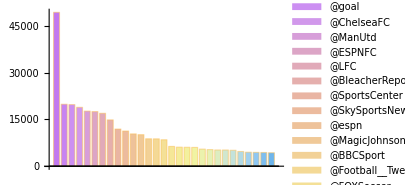

```mathematica
Clear[othersUSN,us,US]
us=Take[usernames[GoodTweetsRT["en"]],29];
othersUSN=Total[usernames[GoodTweetsRT["en"]][[All,2]]]-Total[us[[All,2]]];
US=us/.{"@tphoto2005"->"@■■■■","@urstrulyMahesh"->"@■■■■","@RahulGandhi"->"@■■■■","@imVkohli"->"@■■■■","@433"->"@■■■■","@iamsrk"->"@■■■■","@queeralamode"->"@■■■■","@afrorevolt"->"@afro■■■■","@drkeishakhan"->"@drkeisha■■■■","@praxisnegra"->"@praxis■■■■","@quilombomodern"->"@quilombo■■■■","@jonasdiandrade"->"@jonas■■■■","@AndressaMDuarte"->"@Andressa■■■■","@Nailahnv"->"@Naila■■■■","@jessicabatan"->"@jessica■■■■"};
BCUMEN=BarChart[us[[All,2]],ImageSize->300,ChartLegends->Take[US[[All,1]],20],ChartStyle->{"Pastel"}]
```

Tabela para os nomes de usuários em espanhol.

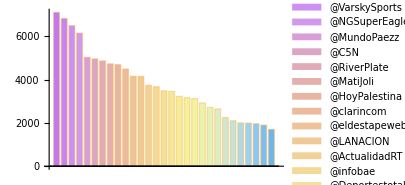

```mathematica
Clear[othersUSN,us,US]
us=Take[usernames[GoodTweetsRT["es"]],29];
othersUSN=Total[usernames[GoodTweetsRT["es"]][[All,2]]]-Total[us[[All,2]]];
US=us/.{"@tphoto2005"->"@■■■■","@urstrulyMahesh"->"@■■■■","@RahulGandhi"->"@■■■■","@imVkohli"->"@■■■■","@433"->"@■■■■","@iamsrk"->"@■■■■","@queeralamode"->"@■■■■","@afrorevolt"->"@afro■■■■","@drkeishakhan"->"@drkeisha■■■■","@praxisnegra"->"@praxis■■■■","@quilombomodern"->"@quilombo■■■■","@jonasdiandrade"->"@jonas■■■■","@AndressaMDuarte"->"@Andressa■■■■","@Nailahnv"->"@Naila■■■■","@jessicabatan"->"@jessica■■■■"};
BCUMEN=BarChart[us[[All,2]],ImageSize->300,ChartLegends->Take[US[[All,1]],20],ChartStyle->{"Pastel"}]
```

Tabela para nomes de usuários mais frequentes nos tweets em português.

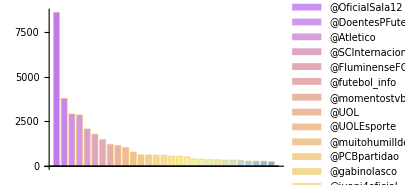

```mathematica
Clear[othersUSN,us,US]
us=Take[usernames[GoodTweetsRT["pt"]],29];
othersUSN=Total[usernames[GoodTweetsRT["pt"]][[All,2]]]-Total[us[[All,2]]];
US=us/.{"@tphoto2005"->"@■■■■","@urstrulyMahesh"->"@■■■■","@RahulGandhi"->"@■■■■","@imVkohli"->"@■■■■","@433"->"@■■■■","@iamsrk"->"@■■■■","@queeralamode"->"@■■■■","@afrorevolt"->"@afro■■■■","@drkeishakhan"->"@drkeisha■■■■","@praxisnegra"->"@praxis■■■■","@quilombomodern"->"@quilombo■■■■","@jonasdiandrade"->"@jonas■■■■","@AndressaMDuarte"->"@Andressa■■■■","@Nailahnv"->"@Naila■■■■","@jessicabatan"->"@jessica■■■■"};
BCUMEN=BarChart[us[[All,2]],ImageSize->300,ChartLegends->Take[US[[All,1]],20],ChartStyle->{"Pastel"}]
```

#### Vamos pesquisar os tweets sem os retweets para ter uma medida diferencial da dimensão da produção de conteúdos e da circulação de conteúdos em relação com Maradona.

```mathematica
Clear[NoRT]
Do[NoRT[j]=Select[GoodTweetsRT[j],Not[StringContainsQ[#,StartOfString~~"RT",IgnoreCase->True]]&],{j,mylang}]
```

```mathematica
TableForm[Table[Length[NoRT[j]],{j,mylang}],TableHeadings->{mylang}]
```

en | 94900
es | 104207
pt | 12370

#### Criamos uma série de regras para construir termos significativos e as aplicamos aos tweets com e sem retweets:

```mathematica
Clear[EncodeRules,DecodeRules]
EncodeRules={"Brazil"->"Brasil",("Buenos Aires"|"Baires"|"BsAs")->"BuenosAires",("Sao Paulo"|"São Paulo"|"San Pablo")->"SaoPaulo",("Rio de Janeiro" |"RioJaneiro"|"RiodeJaneiro")->"RioDeJaneiro",("NYC" |"New York City"|"NewYorkCity"|"NewYork"|"Nova Yorque"|"New York"|"Nueva York"|"Nova York")->"NewYork",("Estados Unidos de América"|"Estados Unidos")->"EstadosUnidos",("United States of America"|"United States")->"UnitedStates",("Latin America"|"Latin American")->"LatinAmerica",("América Latina"|"Latino América"|"Latinoamérica")->"AméricaLatina",("Diego Maradona"|"DiegoMaradona"|"Dieguito Maradona")->"DiegoMaradona","Casa Rosada"->"CasaRosada",("Mané Garrincha"|"Manoel Garrincha")->"ManoelGarrincha",("Lionel Messi"|"Leonel Messi"|"Leo Messi"|"Lio Messi")->"LionelMessi","Boca Juniors"->"BocaJuniors",("Fidel Castro"|"fidelcastro")->"FidelCastro",("Nicolás Maduro"|"Nicolas Maduro")->"NicolasMaduro",("Cristina Kirchner"|"Cristina C. Kirchner")->"CristinaKirchner","Kobe Bryant"->"KobeBryant","Chadwick Boseman"->"ChadwickBoseman","All Blacks"->"AllBlacks"};
DecodeRules={"BuenosAires"->"Buenos Aires","SaoPaulo"->"São Paulo","RioDeJaneiro"->"Rio de Janeiro","NewYork"->"New York","EstadosUnidos"->"Estados Unidos","UnitedStates"->"United States","LatinAmerica"->"Latin America","AméricaLatina"->"América Latina","DiegoMaradona"->"Diego Maradona","CasaRosada"->"Casa Rosada","ManoelGarrincha"->"Manoel Garrincha","LionelMessi"->"Lionel Messi","BocaJuniors"->"Boca Juniors","FidelCastro"->"Fidel Castro","NicolasMaduro"->"Nicolas Maduro","CristinaKirchner"->"Cristina Kirchner","KobeBryant"->"Kobe Bryant","ChadwickBoseman"->"Chadwick Boseman","AllBlacks"->"All Blacks"};
```

```mathematica
Clear[EncRT,EncNoRT]
Do[EncRT[j]=Map[{StringReplace[#[[1]],EncodeRules,IgnoreCase->True],#[[2]]}&,Tally[GoodTweetsRT[j]]],{j,mylang}];
Do[EncNoRT[j]=Map[{StringReplace[#[[1]],EncodeRules,IgnoreCase->True],#[[2]]}&,Tally[NoRT[j]]],{j,mylang}];
```

```mathematica
RandomChoice[EncNoRT["es"]]
```

{El Diego político: Maradona sí se mancha | https://t.co/s1q73oMc2M,1}

### Operações adicionais de “limpeza” dos tweets com o objetivo de construir uma nuvem de palavras com os termos mais frequentes no córpus.

### Fazemos uma “limpeza” de links, nomes de usuários e outros caracteres não alfanuméricos no córpus.

```mathematica
Clear[CleanText,ProperWords]
CleanText[text_]:=StringReplace[text,{RegularExpression["[http]*[s]*[:][\\/\\/][a-z0-9.\\/]+[ ]*"]->" ",RegularExpression["[rt: ]*[rt ]*[\\@][a-z0-9]*[:]*"]->" ",RegularExpression["@[a-z0-9]*[:]*"]->" "},IgnoreCase->True];
ProperWords[lw_]:=Select[lw,And[StringFreeQ[#,RegularExpression["\\W"]],StringLength[#]>4]&];
```

```mathematica
Clear[ttweetsRT,ttweetsNoRT]
Do[ttweetsRT[j]=SortBy[Map[{ProperWords[TextWords[CleanText[#[[1]]]]],#[[2]]}&,EncRT[j]],-#[[2]]&],{j,mylang}];
Do[ttweetsNoRT[j]=SortBy[Map[{ProperWords[TextWords[CleanText[#[[1]]]]],#[[2]]}&,EncNoRT[j]],-#[[2]]&],{j,mylang}];
```

```mathematica
RandomChoice[ttweetsNoRT["pt"],3]
```

{{{Futebol,Diego,Maradona,faleceu},1},{{diego,maradona,morreu},1},{{Diego,Maradona,história,futebol,mundial,chegou,segundo,história},1}}

```mathematica
Length[ttweetsRT["pt"]]
```

14590

```mathematica
TableForm[Outer[Length[ttweetsRT[#1]]&,mylang],TableHeadings->{mylang}]
```

en | 111450
es | 118160
pt | 14590

#### Partindo de uma lista de stopwords, ou palavras sem valor léxico, (artigos, pronomes, preposições) em português, inglês e espanhol (artigos, pronomes, preposições) em português, inglês e espanhol (disponíveis em http://snowball.tartarus.org/algorithms/portuguese/stop.txt, http://snowball.tartarus.org/algorithms/spanish/stop.txt e http://snowball.tartarus.org/algorithms/english/stop.txt e com acréscimos próprios), eliminamos todas essas palavras de nosso córpus.

```mathematica
Clear[swes,swpt,swen,stopwords,RemoveStopWords,cleantweetsNoRT0,cleantweetsRT0]
swes=Get[path<>"dictionaries\\sw-es.txt"];
swpt=Get[path<>"dictionaries\\sw-pt.txt"];
swen=Get[path<>"dictionaries\\sw-en.txt"];
stopwords=Join[swes,swpt,swen];
RemoveStopWords[s_]:=Select[s,Not[StringMatchQ[#,Alternatives@@stopwords,IgnoreCase->True]]&];
Do[cleantweetsRT0[j]=Map[{RemoveStopWords[#[[1]]],#[[2]]}&,ttweetsRT[j]],{j,mylang}];
Do[cleantweetsNoRT0[j]=Map[{RemoveStopWords[#[[1]]],#[[2]]}&,ttweetsNoRT[j]],{j,mylang}];
```

```mathematica
RandomChoice[cleantweetsRT0["es"],4]
```

{{{juzgan,deben,juzgados,humanidad,Diego,Maradona,bendecidos},1},{{27Nov,coincidencia,muerte,Diego,Maradona,amigo,Fidel,Castro},1},{{DIEGO,MARADONA,CUMPLO,MUERTO,PASAS,DORMIRE,CREES,BUSCALO,GOOGLE,DIEMGOM,MARAMDONAM,MANDA,IGNORÓ,MURIÓ},3},{{muerte,Diego,Maradona,Matías,Morla,acusó,personal,salud},1}}

#### Depois consolidamos nosso corpus agrupando aqueles tweets que tenham ficado iguais após a eliminação das stopwords.

```mathematica
Clear[ConsolidateTally,cleantweetsNoRT,cleantweetsRT]
ConsolidateTally[tally_]:=Map[{#[[1,1]],Total[#[[All,2]]]}&,Gather[tally,SameQ[#1[[1]],#2[[1]]]&]];
Do[cleantweetsNoRT[j]=ConsolidateTally[cleantweetsRT0[j]],{j,mylang}];
Do[cleantweetsRT[j]=ConsolidateTally[cleantweetsNoRT0[j]],{j,mylang}];
```

### A última operação de limpeza tem a ver com obter as raízes das palavras nas três línguas e agrupar as palavras de acordo com a palavra mais frequente da mesma raiz

Primeiro computamos a quantidade de repetições das palavras com uma função que considera a multiplicidade de tweets.

```mathematica
Clear[DistributeList,ConsolidateTally,wordtallyNoRT,wordtallyRT]
DistributeList[{l_List,x_}]:=Map[{#,x}&,l];
ConsolidateTally[tally_]:=Map[{#[[1,1]],Total[#[[All,2]]]}&,Gather[tally,SameQ[#1[[1]],#2[[1]]]&]];
Do[wordtallyNoRT[j]=SortBy[ConsolidateTally[Join@@Map[DistributeList,cleantweetsNoRT[j]]],-#[[2]]&],{j,mylang}];
Do[wordtallyRT[j]=SortBy[ConsolidateTally[Join@@Map[DistributeList,cleantweetsRT[j]]],-#[[2]]&],{j,mylang}];
```

Definimos um comando que obtém o termo mais comum de uma classe de termos para cada língua. Fazemos isso através das funções WordStem, WordStemES e WordStemPT. A primeira é uma função de Wolfram que obtém a raiz das palavras. As duas últimas foram implementadas por nós no Wolfram Mathematica a partir do algoritmo para obter raízes dessas línguas presente aqui: http://snowball.tartarus.org/algorithms/portuguese/stemmer.html e http://snowball.tartarus.org/algorithms/spanish/stemmer.html.

```mathematica
Clear[MeaningfulTermsRules]
MeaningfulTermsRules[ts_,"en"]:=Module[{cat,f},
cat=Gather[ts,SameQ[WordStem[ToLowerCase[#1[[1]]]],WordStem[ToLowerCase[#2[[1]]]]]&];
f[c_]:=Map[#[[1]]->Last[SortBy[c,Last]][[1]]&,c];
Select[Union[Flatten[Map[f,cat]]],Not[SameQ[#[[1]],#[[2]]]]&]];
MeaningfulTermsRules[ts_,"es"]:=Module[{cat,f},
cat=Gather[ts,SameQ[WordStemES[ToLowerCase[#1[[1]]]],WordStemES[ToLowerCase[#2[[1]]]]]&];
f[c_]:=Map[#[[1]]->Last[SortBy[c,Last]][[1]]&,c];
Select[Union[Flatten[Map[f,cat]]],Not[SameQ[#[[1]],#[[2]]]]&]];
MeaningfulTermsRules[ts_,"pt"]:=Module[{cat,f},
cat=Gather[ts,SameQ[WordStemPT[ToLowerCase[#1[[1]]]],WordStemPT[ToLowerCase[#2[[1]]]]]&];
f[c_]:=Map[#[[1]]->Last[SortBy[c,Last]][[1]]&,c];
Select[Union[Flatten[Map[f,cat]]],Not[SameQ[#[[1]],#[[2]]]]&]];
```

Geramos uma série de regras de transformação das palavras a partir de nosso corpus dos tweets em diferentes línguas.

```mathematica
Clear[mrulesNoRT,mrulesRT]
Do[mrulesNoRT[j]=MeaningfulTermsRules[wordtallyNoRT[j],j],{j,mylang}];
Do[mrulesRT[j]=MeaningfulTermsRules[wordtallyRT[j],j],{j,mylang}];
```

```mathematica
mrulesNoRT["pt"]
```

{2022Presidente→2022PRESIDENTE,21H30→21h30,Abaixo→abaixo,abala→abalou,abalada→abalou,abalado→abalou,abalados→abalou,abalar→abalou,abalará→abalou,abandonado→abandono,abandonam→abandono,abandonar→abandono,abandonou→abandono,abatido→abatidos,aberta→aberto,ABERTA→aberto,abertas→aberto,5732,volte→volta,voltei→volta,Voltei→volta,volto→volta,voltou→volta,votar→votou,votaram→votou,votaria→votou,vulgar→vulgo,world→World,xingando→xingar,youtube→YouTube,Youtube→YouTube,YOUTUBE→YouTube,zmarł→Zmarł,zueira→zueiras}
 |  |  |  |

```mathematica
RandomChoice[mrulesRT["en"],20]
```

{FARMERS→farmers,Redemption→redemption,confirmation→confirmed,scooped→scoop,originally→original,newscast→Newscast,SENOR→Senor,Grand→grand,Playmaker→playmaker,spanning→spans,driving→drive,directors→director,Studio→studio,POLITICAL→politics,Diegos→Diego,Middle→middle,accepting→accept,NIALL→Niall,REMEMBER→remember,protecting→protect}

Vamos substituir as palavras pela palavra mais frequente do grupo dado pela mesma raiz, de acordo com as regras já computadas.

```mathematica
Clear[mtweetsNoRT,mtweetsRT]
Do[mtweetsNoRT[j]=Map[{Sort[#[[1]]],#[[2]]}&,Replace[cleantweetsNoRT[j],mrulesNoRT[j],{3}]],{j,mylang}];
Do[mtweetsRT[j]=Map[{Sort[#[[1]]],#[[2]]}&,Replace[cleantweetsRT[j],mrulesRT[j],{3}]],{j,mylang}];
```

```mathematica
RandomChoice[mtweetsRT["pt"],4]
```

{{{atenção,atleta,braço,conservadores,Diego,fenomenal,Fidel,filho,generoso,gigante,Guevara,homenagear,Maradona,Plantão,Saiba,sentir,simpatia,social,tatuagem},1},{{argentino,Diego,imprensa,Maradona,morre},1},{{argentino,Diego,espera,feriado,Maradona,morre,viram},1},{{argentino,brabo,Diego,futebol,ídolo,Maradona,perda},1}}

Vamos computar as palavras que só aparecem uma vez em cada conjunto de tweets (por língua), que consideraremos triviais para obtenção dos temas principais.

```mathematica
Clear[trivialwordsNoRT,trivialwordsRT]
Do[trivialwordsNoRT[j]=Select[Tally[Flatten[mtweetsNoRT[j][[All,1]]]],#[[2]]<2&][[All,1]],{j,mylang}];
Do[trivialwordsRT[j]=Select[Tally[Flatten[mtweetsRT[j][[All,1]]]],#[[2]]<2&][[All,1]],{j,mylang}];
```

Computamos os tweets significativos eliminando as palavras que aparecem só uma vez, as quais consideraremos triviais para extrair os temas principais.

```mathematica
Clear[MtweetsNoRT,MtweetsRT]
Do[MtweetsNoRT[j]=ConsolidateTally[Select[Map[{Sort[Complement[#[[1]],trivialwordsNoRT[j]]],#[[2]]}&,mtweetsRT[j]],Length[#]≥1&]],{j,mylang}];
Do[MtweetsRT[j]=ConsolidateTally[Select[Map[{Sort[Complement[#[[1]],trivialwordsRT[j]]],#[[2]]}&,mtweetsRT[j]],Length[#]≥1&]],{j,mylang}];
```

```mathematica
Clear[mwordsNoRT,mwordsRT]
Do[mwordsNoRT[j]=SortBy[ConsolidateTally[Join@@Map[DistributeList,MtweetsNoRT[j]]],-#[[2]]&],{j,mylang}];
Do[mwordsRT[j]=SortBy[ConsolidateTally[Join@@Map[DistributeList,MtweetsRT[j]]],-#[[2]]&],{j,mylang}];
```

Guardando nossos processamentos feitos até agora.

```mathematica
Do[Put[{ttweetsRT[j],cleantweetsRT0[j],cleantweetsRT[j],wordtallyRT[j],mrulesRT[j],trivialwordsRT[j],MtweetsRT[j],mtweetsRT[j],mwordsRT[j],ttweetsNoRT[j],cleantweetsNoRT0[j],cleantweetsNoRT[j],wordtallyNoRT[j],mrulesNoRT[j],trivialwordsNoRT[j],MtweetsNoRT[j],mtweetsNoRT[j],mwordsNoRT[j]},path<>"output\\Maradona_processed_tweets-"<>ToString[j]<>".dat"],{j,mylang}];
```

Recuperando nossos processamentos feitos até agora.

```mathematica
Clear[mylang,ttweetsRT,cleantweetsRT0,cleantweetsRT,wordtallyRT,mrulesRT,trivialwordsRT,MtweetsRT,mtweetsRT,mwordsRT,ttweetsNoRT,cleantweetsNoRT0,cleantweetsNoRT,wordtallyNoRT,mrulesNoRT,trivialwordsNoRT,MtweetsNoRT,mtweetsNoRT,mwordsNoRT];
mylang={"en","es","pt"};
Do[{ttweetsRT[j],cleantweetsRT0[j],cleantweetsRT[j],wordtallyRT[j],mrulesRT[j],trivialwordsRT[j],MtweetsRT[j],mtweetsRT[j],mwordsRT[j],ttweetsNoRT[j],cleantweetsNoRT0[j],cleantweetsNoRT[j],wordtallyNoRT[j],mrulesNoRT[j],trivialwordsNoRT[j],MtweetsNoRT[j],mtweetsNoRT[j],mwordsNoRT[j]}=Get[path<>"output\\Maradona_processed_tweets-"<>ToString[j]<>".dat"],{j,mylang}];
```

Tabelas para o número de tweets significativos únicos, com ou sem retweets:

```mathematica
TableForm[Table[Length[MtweetsNoRT[j]],{j,mylang}],TableHeadings->{mylang}]
TableForm[Table[Length[MtweetsRT[j]],{j,mylang}],TableHeadings->{mylang}]
```

en | 48397
es | 59535
pt | 8798

en | 48345
es | 59480
pt | 8791

### Com os processamentos resultantes, elaboramos Nuvens de Palavras.

```mathematica
Do[mywcRT[j]=WordCloud[mwordsRT[j][[3;;400]],PlotTheme->"Web",MaxItems->400,WordOrientation->"HorizontalVertical",ImageSize->500];Put[mywcRT[j],path<>"output\\mywcRT-"<>"-"<>j<>".dat"];Print["Done RT: "<>j];,{j,mylang}]
```

Done RT: en

Done RT: es

Done RT: pt

```mathematica
Do[mywcRT[j]=Get[path<>"output\\mywcRT-"<>"-"<>j<>".dat"],{j,mylang}]
```

```mathematica
Do[Export[path<>"output\\mywcRTpicture-"<>j<>".png",mywcRT[j]],{j,mylang}];
```

```mathematica
Clear[mywcRTimage]
Do[mywcRTimage[j]=Import[path<>"output\\mywcRTpicture-"<>j<>".png"],{j,mylang}];
```

Nuvem de palavras para os tweets sobre Maradona em inglês

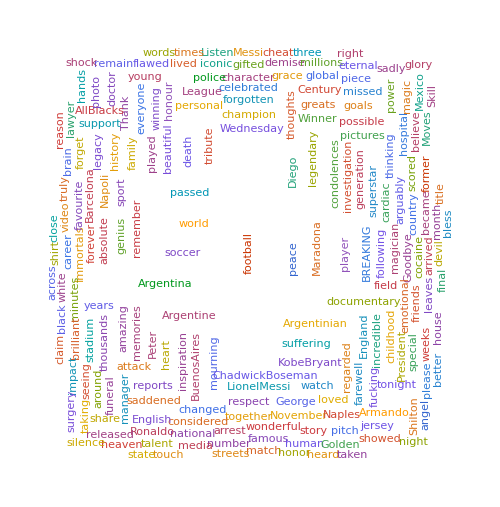

```mathematica
WordCloud[mwordsRT["en"][[3;;400]],PlotTheme->"Web",MaxItems->200,WordOrientation->"HorizontalVertical",ImageSize->500]
```

Nuvem de palavras para os tweets sobre Maradona em espanhol

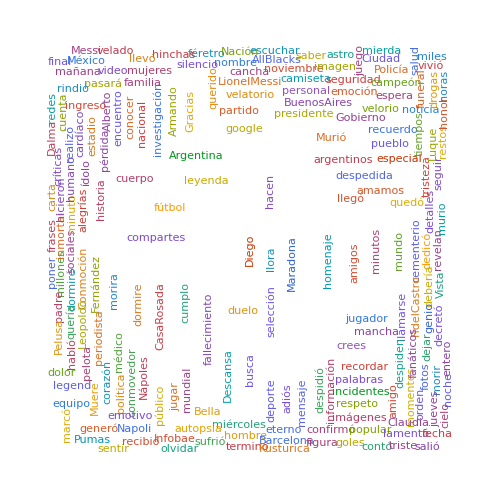

```mathematica
WordCloud[mwordsRT["es"][[3;;400]],PlotTheme->"Web",MaxItems->200,WordOrientation->"HorizontalVertical",ImageSize->500]
```

Nuvem de palavras para os tweets sobre Maradona em português

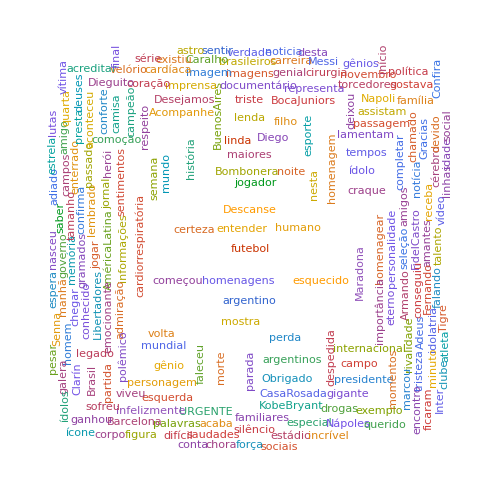

```mathematica
WordCloud[mwordsRT["pt"][[3;;400]],PlotTheme->"Web",MaxItems->200,WordOrientation->"HorizontalVertical",ImageSize->500]
```